# Search Advertising: Numerical analysis

Model: demand function, consumer type, and profit

```mathematica
Demand[theta_, p_, pbar_, eta_]:= Piecewise[{{0, p > pbar}},theta + p^(-eta)]
InverseDemand[theta_, q_, eta_]:= Piecewise[{{0, theta >q}},(q-theta)^(-1/eta)]
CdfTheta[theta_, gamma_]:=Piecewise[{{0, theta <0}, {1, theta > 1}}, theta^gamma]
PdfTheta[theta_, gamma_]=D[CdfTheta[theta, gamma],theta] 
Profit[theta_, p_, pbar_, eta_]:= Piecewise[{{0, p>pbar }},(p-0.2)*Demand[theta, p, pbar, eta]]
DerivativeProfit[theta_, p_,pbar_, eta_]=D[Profit[theta,p,pbar,eta],p]
```

Piecewise[{{0, theta<0}, {gamma theta^(-1+gamma), 0<theta<1}, {0, theta>1}, {Indeterminate, True}}]

Piecewise[{{0, p-pbar>0}, {(eta (-0.2+p) theta)/p-eta (-0.2+p) p^(-1-eta) (1.+p^eta theta)+p^-eta (1.+p^eta theta), True}}]

```mathematica
Demand[1, 1/5, 1, 2]
InverseDemand[1, 26, 2]
Profit[1,1/5,1,2]
CdfTheta[0.5,0.5]
```

26

1/5

0.

0.707107

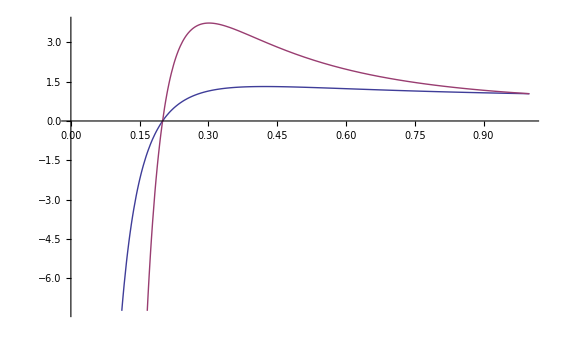

```mathematica
Plot[{Profit[0.3, p, 1.0,2.0],Profit[0.3, p, 1.0,3.0]},{p,0,1}]
```

First order condition (Privacy)

```mathematica
FirstOrderCondition[p_, pbar_, eta_, gamma_]:=Integrate[DerivativeProfit[theta, p, pbar, eta]*PdfTheta[theta, gamma] ,{theta, 0, 1}]
FullSimplify[FirstOrderCondition[p, pbar, eta, gamma]]
FirstOrderCondition[0.202779, 1.0, 2.0, 0.5]
```

Piecewise[{{Piecewise[{{(0.2 p^(-1.-1. eta) (eta+eta gamma+5. p-5. eta p+5. gamma p-5. eta gamma p+5. gamma p^(1.+eta)))/(1.+gamma), Re[gamma]>0.}, {Integrate[0.2 gamma p^(-1.-1. eta) theta^(-1.+gamma) (eta+5. p-5. eta p+5. p^(1.+eta) theta),{theta,0.,1.},Assumptions→p-1. pbar≤0.&&Re[gamma]≤0.], True}}], p-1. pbar≤0.}, {0., True}}]

23.9862

Results: Profit, CS, Welfare

```mathematica
ExpectedTheta[gamma_]:=Integrate[theta*D[CdfTheta[theta, gamma], theta],{theta,0,1}]
ExpectedProfit[p_, pbar_, eta_, gamma_]:=Integrate[Profit[theta,p,pbar,eta]*D[CdfTheta[theta, gamma], theta], {theta, 0, 1}]
ExpectedConsumerSurplus[theta_, qstar_, eta_]:=Integrate[InverseDemand[theta, q, eta],{q, 0, qstar}]
FullSimplify[ExpectedProfit[p, pbar, eta, gamma]]
ExpectedTheta[0.5]
ExpectedProfit[0.2, 1.0, 2.0, 0.5]
ExpectedConsumerSurplus[ExpectedTheta[0.5],26, 2.0]
```

Piecewise[{{Piecewise[{{(0.2 p^(-1. eta) (-1.+5. p) (1.+gamma+gamma p^eta))/(1.+gamma), Re[gamma]>0.}, {Integrate[0.2 gamma p^(-1. eta) (-1.+5. p) theta^(-1.+gamma) (1.+p^eta theta),{theta,0.,1.},Assumptions→p-1. pbar≤0.&&Re[gamma]≤0.], True}}], p-1. pbar≤0.}, {0., True}}]

1/3

0.

10.1325

Computation of equilibria: Tests (no need to redo)

```mathematica
NSolve[FirstOrderCondition[p, 1.0, 2.0, 0.5] == 0, p]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

{{p→1.-1. UnitStep^(-1)[0.]},{p→-1.90522},{p→0.425719},{p→1.4795}}

Solving for various gamma (higher gamma: higher density of consumers towards gamma value 1)

```mathematica
Quiet[For[i=0.5,i<=1.5,i+=0.25,Print[i , NSolve[FirstOrderCondition[p , 1.0, 2.0, i] == 0, p]]]]
```

0.5{{p→1.-1. UnitStep^(-1)[0.]},{p→-1.90522},{p→0.425719},{p→1.4795}}

0.75{{p→1.-1. UnitStep^(-1)[0.]},{p→-1.69795},{p→0.435366},{p→1.26258}}

1.{{p→1.-1. UnitStep^(-1)[0.]},{p→-1.58285},{p→0.443665},{p→1.13919}}

1.25{{p→1.-1. UnitStep^(-1)[0.]},{p→-1.50902},{p→0.450944},{p→1.05807}}

1.5{{p→1.-1. UnitStep^(-1)[0.]},{p→-1.45743},{p→0.457427},{p→1.}}

Solving for various eta

```mathematica
Quiet[For[i=2.0,i≤3.0,i+=0.25,Print[i , NSolve[FirstOrderCondition[p , 1.0, i, 1] == 0, p]]]]
```

2.{{p→1.-1. UnitStep^(-1)[0.]},{p→-1.58285},{p→0.443665},{p→1.13919}}

2.25{{p→1.-1. UnitStep^(-1)[0]},{p→-1.55113-0.519853 ⅈ},{p→-1.55113+0.519853 ⅈ},{p→0.37676},{p→1.30121}}

2.5{{p→1.-1. UnitStep^(-1)[0]},{p→-1.37438-0.920261 ⅈ},{p→-1.37438+0.920261 ⅈ},{p→0.341056},{p→1.39074}}

2.75{{p→1.-1. UnitStep^(-1)[0]},{p→-1.13694-1.20062 ⅈ},{p→-1.13694+1.20062 ⅈ},{p→0.318185},{p→1.4422}}

3.{{p→1.-1. UnitStep^(-1)[0.]},{p→-0.886643-1.38347 ⅈ},{p→-0.886643+1.38347 ⅈ},{p→0.302082},{p→1.47121}}

Order statistics

```mathematica
PdfOrderStat[x_,k_,n_, gamma_]:= (n!)/((k-1)!*(n-k)!)*CdfTheta[x, gamma]^(k-1)*(1-CdfTheta[x, gamma])^(n-k)*PdfTheta[x, gamma]
CdfOrderStat[y_,k_,n_,gamma_] = Integrate[PdfOrderStat[x,k,n,gamma], {x,0,y}]
```

∫_0^y (n! (1-Piecewise[{{0, x<0}, {1, x>1}, {x^gamma, True}}])^(-k+n) (Piecewise[{{0, x<0}, {1, x>1}, {x^gamma, True}}])^(-1+k) (Piecewise[{{0, x<0}, {gamma x^(-1+gamma), 0<x<1}, {0, x>1}, {Indeterminate, True}}]))/((-1+k)! (-k+n)!)ⅆx

```mathematica
PdfOrderStat[0.5,3,4,0.5]
Integrate[PdfOrderStat[x,3,4,0.5], {x,0,0.5}]
CdfOrderStat[0.5,3,4,0.5]
Integrate[PdfOrderStat[x,2,4,0.5], {x,0,0.5}]
CdfOrderStat[0.5,2,4,0.5]
```

1.24264

0.664214

0.664214

0.921573

0.921573

```mathematica
CdfTheta[0.4,0.5]
CdfOrderStat[0.4,2,2,0.5]
CdfOrderStat[0.4,1,2,0.5]
```

0.632456

0.4

0.864911

Reading:
Proba that the kth highest draw is below y. With gamma as 0.5 and only one draw, the probability to have a theta lower than 0.4 is c. 0.63. 
With the same gamma and two draws: the proba that the highest of both (the 2nd of 2) is below 0.4 is 0. 4(<0.63) and the proba that the lowest (the 1st of 2) is below 0.4 is c. 0.86.

First order condition (Disclosure)

```mathematica
FirstOrderConditionDisclosure[p_, pbar_, eta_, gamma_,k_,n_]:=Integrate[DerivativeProfit[theta, p, pbar, eta]*PdfTheta[theta, gamma]* CdfOrderStat[theta,k,n,gamma],{theta, 0, 1}]
```

Computation of equilibria (Disclosure) : Tests

```mathematica
FirstOrderConditionDisclosure[0.21,1.0,2.0,0.5,4,9]
FindRoot[FirstOrderConditionDisclosure[p, 1.0,2.0,0.5,4,9] == 0, {p,0.1}]
FindRoot[FirstOrderConditionDisclosure[p, 1.0,2.0,10,9,9] == 0, {p,0.1}]
FindRoot[FirstOrderConditionDisclosure[p, 1.0,2.0,0.5,5,9] == 0, {p,0.1}]
FindRoot[FirstOrderConditionDisclosure[p, 1.0,2.0,0.5,15,15] == 0, {p,0.1}]
```

12.6127

{p→0.444294}

{p→2.03665}

{p→0.451649}

{p→0.539856}

```mathematica
Quiet[For[i=0.1,i≤2.1,i+=0.5,Print[i , FindRoot[FirstOrderConditionDisclosure[p, 1.0,2.0,i,5,9] == 0, {p,0.1}]]]]
```

0.1{p→0.201475}

0.6{p→0.205259}

1.1{p→0.206582}

1.6{p→0.207237}

2.1{p→0.207626}

```mathematica
Quiet[For[i=2.0,i≤3.0,i+=0.5,Print[{i , FindRoot[FirstOrderConditionDisclosure[p, 1.0,i,0.5,5,9] == 0, {p,0.1}]}]]]
```

{2.,{p→0.204817}}

{2.5,{p→0.167384}}

{3.,{p→0.150142}}

Graphs

```mathematica
Manipulate[Plot[ExpectedProfit[p, 1, eta, gamma], {p,0,1}],{eta,2,3}, {gamma,0.5,3}]
```

Output for privacy

```mathematica
Do[{Print[ {i,j}]},{i,0.5,1.5,0.5}, {j, 2.0, 3.0, 0.5}];
```

```mathematica
dim=Apply[Times,Dimensions[Table[0, {i,0.5,1.5,0.25}, {j, 2.0, 3.0, 0.25}]]]
arparam = Range[dim];
arresult=Range[dim];
arprofit = Range[dim];
arcsurplus = Range[dim];
count = 0;
Quiet[Do[{count = count + 1,
arsol = NSolve[FirstOrderCondition[p , 1.0, j, i] == 0 , p],
sol = Select[p/.arsol, #≥0 && #≤ 1&] ,
arresult[[count]]=sol[[1]],
arparam[[count]] = {i,j},
arprofit[[count]]=ExpectedProfit[arresult[[count]], 1.0, j, i],
etheta=ExpectedTheta[i],
eqstar =Demand[etheta, sol[[1]], 1.0, j],
arcsurplus[[count]]=ExpectedConsumerSurplus[etheta, eqstar, j]},{i,0.5,1.5,0.25},{j, 2.0, 3.0, 0.25}]]
```

25

```mathematica
arparam
arresult
arprofit
arcsurplus
Partition[arresult,5]
```

{{0.5,2.},{0.5,2.25},{0.5,2.5},{0.5,2.75},{0.5,3.},{0.75,2.},{0.75,2.25},{0.75,2.5},{0.75,2.75},{0.75,3.},{1.,2.},{1.,2.25},{1.,2.5},{1.,2.75},{1.,3.},{1.25,2.},{1.25,2.25},{1.25,2.5},{1.25,2.75},{1.25,3.},{1.5,2.},{1.5,2.25},{1.5,2.5},{1.5,2.75},{1.5,3.}}

{0.425719,0.370589,0.33834,0.316844,0.301375,0.435366,0.37403,0.339873,0.317605,0.301777,0.443665,0.37676,0.341056,0.318185,0.302082,0.450944,0.378981,0.341997,0.318642,0.30232,0.457427,0.380826,0.342764,0.31901,0.302512}

{1.32068,1.64886,2.12373,2.79496,3.73726,1.34262,1.66527,2.13697,2.80613,3.74694,1.35972,1.6778,2.14701,2.81455,3.75422,1.37346,1.68768,2.15487,2.82113,3.7599,1.38475,1.69568,2.1612,2.82641,3.76445}

{4.69794,6.22524,8.46875,11.7439,16.5149,4.59384,6.15374,8.41152,11.6948,16.4709,4.5079,6.09806,8.36778,11.6575,16.4377,4.43514,6.05341,8.33326,11.6283,16.4118,4.37228,6.01679,8.30531,11.6048,16.391}

{{0.425719,0.370589,0.33834,0.316844,0.301375},{0.435366,0.37403,0.339873,0.317605,0.301777},{0.443665,0.37676,0.341056,0.318185,0.302082},{0.450944,0.378981,0.341997,0.318642,0.30232},{0.457427,0.380826,0.342764,0.31901,0.302512}}

```mathematica
ListPlot3D[Partition[arresult,5],DataRange->{{2.0,3.0},{0.5,1.5}}]
```

-Graphics3D-

With eta increasing from 0.5 to 1.5, optimal price slightly increases as demand elasticity is decreased (increase marginal cost to have it more visible?). With gamma increasing from two to three, price increases significantly as a result of a shift in the distribution towards higher values of theta i.e. an increase in the proportion of high value consumers.

```mathematica
arprofit+arcsurplus
```

{6.01862,7.8741,10.5925,14.5389,20.2522,5.93646,7.81901,10.5485,14.5009,20.2179,5.86763,7.77586,10.5148,14.472,20.192,5.8086,7.74109,10.4881,14.4494,20.1717,5.75704,7.71246,10.4665,14.4312,20.1554}

```mathematica
ListPlot3D[Partition[arprofit+arcsurplus,5],DataRange->{{2.0,3.0},{0.5,1.5}}]
```

-Graphics3D-

Output for disclosure

Do it on k and n... (since pretty clear for eta gamma a priori...)